# 0) Preliminaries

```mathematica
plotFun[fun_,lims_,epilog_,label_,legs_:None]:=Framed@Plot[fun,{x,lims[[1,1]],lims[[1,2]]},PlotRange->{Full,{lims[[2,1]],lims[[2,2]]}},Epilog->epilog,PlotLegends->legs,PlotLabel->Style[label,Black,Bold,20],ImageSize->Large,AxesLabel->{"x","y"},BaseStyle->{FontSize->20}]
```

```mathematica
discPlotFun[fun_,range_,lims_,epilog_,label_]:=Framed@DiscretePlot[fun,{n,range[[1]],range[[2]]},PlotRange->lims,Epilog->epilog,PlotLabel->Style[label,Black,Bold,20],ImageSize->Large,AxesLabel->{"M","y"},BaseStyle->{FontSize->20}]
```

```mathematica
(*ClearAll[plotLimitDisc]
plotLimitDisc[fun_,n0fun_,epsran_,maxran_,limit_,label_,seqname_:"a_n",epilog_:{},limpos_:Automatic]:=Module[{funplot,epsplot,ilimpos=limpos},
If[ilimpos===Automatic,ilimpos={22,limit+05}];
funplot=DiscretePlot[fun[n],{n,1,maxran},PlotRange->{Full,All},Filling->None,Epilog->epilog,PlotLabel->Style[label,Black,Bold,20],ImageSize->Large,AxesLabel->{"n","y"},BaseStyle->{FontSize->20}];
epsplot[ϵ_]:=Graphics[{{Line[{{1,limit},{maxran,limit}}],Arrow[{ilimpos-{0.5,0}(*{(*maxran-20*)20,limit+.05}*),{(*maxran-25*)(*15*)ilimpos[[1]]-5,limit}}],Text["lim_(n → ∞) "<>seqname<>"="<>ToString[limit],ilimpos(*{(*maxran-20*)22,limit+.05}*),Left]},{Thick,Orange,Line[{{0,limit-ϵ},{maxran,limit-ϵ}}]},{Arrowheads[{-.03,.03}],Arrow[{{5,limit},{5,limit-ϵ}}],Text[Style["ϵ",20],{4,limit-ϵ/2}]},{Opacity[.5],Orange,Rectangle[{0,limit-ϵ},{maxran,limit}]},Module[{n0=n0fun[ϵ]},{Line[{{n0,fun[n0]},{n0,0}}],Text[Style["n_0= "<>ToString[n0fun[ϵ]],20],{n0+1.5,.05},Left]}]}];
Manipulate[
Column[{
Show[funplot,epsplot[ϵ],epilog,PlotRange->{{0,maxran},All}],
Item[Style["ϵ = "<>ToString[ϵ],30],ItemSize->{All,4},Background->LightOrange]
},Frame->All],
{{ϵ,epsran[[2]]},epsran[[1]],epsran[[2]],Appearance->"Open" }
]
]*)
```

```mathematica
(*ClearAll[plotLimitDisc]
plotLimitDisc[fun_,n0fun_,epsran_,maxran_,limit_,label_,upreg_:True,lowreg_:True,seqname_:"a_n",epilog_:{},limpos_:Automatic]:=Module[{funplot,epsplot,ilimpos=limpos},
If[ilimpos===Automatic,ilimpos={22,limit+05}];
funplot=DiscretePlot[fun[n],{n,1,maxran},PlotRange->{Full,All},Filling->None,Epilog->epilog,PlotLabel->Style[label,Black,Bold,20],ImageSize->Large,AxesLabel->{"n","y"},BaseStyle->{FontSize->20}];
epsplot[ϵ_]:=Graphics[{
(*limit line and label*)
{Line[{{1,limit},{maxran,limit}}],Arrow[{ilimpos-{0.5,0},{ilimpos[[1]]-5,limit}}],Text["lim_(n → ∞) "<>seqname<>"="<>ToString[limit],ilimpos,Left]},

(*lower region*)
If[upreg,{{Thick,Orange,Line[{{0,limit-ϵ},{maxran,limit-ϵ}}]},{Arrowheads[{-.03,.03}],Arrow[{{5,limit},{5,limit-ϵ}}],Text[Style["ϵ",20],{4,limit-ϵ/2}]},{Opacity[.5],Orange,Rectangle[{0,limit-ϵ},{maxran,limit}]}},{}],

(*upper region*)
If[lowreg,{{Thick,Orange,Line[{{0,limit+ϵ},{maxran,limit+ϵ}}]},{Arrowheads[{-.03,.03}],Arrow[{{5,limit},{5,limit+ϵ}}],Text[Style["ϵ",20],{4,limit+ϵ/2}]},{Opacity[.5],Orange,Rectangle[{0,limit+ϵ},{maxran,limit}]}},{}],

(*moving n0*)
Module[{n0=n0fun[ϵ]},{Line[{{n0,fun[n0]},{n0,0}}],Text[Style["n_0= "<>ToString[n0fun[ϵ]],20],{n0+1.5,.05},Left]}]
}];
Manipulate[
Column[{
Show[funplot,epsplot[ϵ],epilog,PlotRange->{{0,maxran},All}],
Item[Style["ϵ = "<>ToString[ϵ],30],ItemSize->{All,4},Background->LightOrange]
},Frame->All],
{{ϵ,epsran[[2]]},epsran[[1]],epsran[[2]],Appearance->"Open" }
]
]*)
```

```mathematica
ClearAll[plotLimitDisc]
plotLimitDisc[fun_,n0fun_,epsran_,maxran_,limit_,label_,upreg_:True,lowreg_:True,seqname_:"a_n",epilog_:{},limpos_:Automatic]:=Module[{funplot,epsplot,ilimpos=limpos},
Manipulate[
Column[{
Show[funplot,epsplot[ϵ],epilog,PlotRange->{{0,maxran},All}],
Item[Style["ϵ = "<>ToString[ϵ],30],ItemSize->{All,4},Background->LightOrange]
},Frame->All],
{{ϵ,epsran[[2]]},epsran[[1]],epsran[[2]],Appearance->"Open" },
{{funplot,DiscretePlot[fun[n],{n,1,maxran},PlotRange->{Full,All},Filling->None,Epilog->epilog,PlotLabel->Style[label,Black,Bold,20],ImageSize->Large,AxesLabel->{"n","y"},BaseStyle->{FontSize->20}]},{0,1},ControlType->None},
{{ilimpos,If[limpos===Automatic,{22,limit+05},limpos]},ControlType->None},
SaveDefinitions->True,Initialization:>{epsplot[ϵ_]:=Graphics[{
(*limit line and label*)
{Line[{{1,limit},{maxran,limit}}],Arrow[{ilimpos-{0.5,0},{ilimpos[[1]]-5,limit}}],Text["lim_(n → ∞) "<>seqname<>"="<>ToString[limit],ilimpos,Left]},

(*lower region*)
If[upreg,{{Thick,Orange,Line[{{0,limit-ϵ},{maxran,limit-ϵ}}]},{Arrowheads[{-.03,.03}],Arrow[{{5,limit},{5,limit-ϵ}}],Text[Style["ϵ",20],{4,limit-ϵ/2}]},{Opacity[.5],Orange,Rectangle[{0,limit-ϵ},{maxran,limit}]}},{}],

(*upper region*)
If[lowreg,{{Thick,Orange,Line[{{0,limit+ϵ},{maxran,limit+ϵ}}]},{Arrowheads[{-.03,.03}],Arrow[{{5,limit},{5,limit+ϵ}}],Text[Style["ϵ",20],{4,limit+ϵ/2}]},{Opacity[.5],Orange,Rectangle[{0,limit+ϵ},{maxran,limit}]}},{}],

(*moving n0*)
Module[{n0=n0fun[ϵ]},{Line[{{n0,fun[n0]},{n0,0}}],Text[Style["n_0= "<>ToString[n0fun[ϵ]],20],{n0+1.5,.05},Left]}]
}]}
]
]
```

# 1) Funktionenfolge

F(x):=∑_(k=1)^∞ (sin(k x))/k^2

a) F_n(x):=∑_(k=1)^n (sin(k x))/k^2 gleichmässig konvergiert?
b) F stetig?
c) F(x+2π)=F(x) ?
d) Plot of F_n ?

G(x):=∑_(k=1)^∞ (sin(k x))/k

e) Plot of G_n ?

#### Useful formulas

Konvergenzkriterium von Weierstraß

f_n:D→ℝ

∑_(n=0)^∞ sup_(x∈D) Abs[f_n(x)]<∞   ⇒   ∑_(n=0)^∞ f_n konvergiert absolut und gleichmässig gegen F:D→ℝ

Satz 10.10.

f_n:D→ℝ stetig   ∧  Folge f_n gleichmässig gegen f: D→ℝ konvergiere   ⇒  f stetig

## Solution

## a)

In the case of F we have:

f_k(x):=(sin(k x))/k^2 with D = ℝ

for which:

sup_(x∈D) Abs[f_n(x)]=sup_(x∈D) Abs[(sin(k x))/k^2]

Function sin(k x) is stetig, therefore assumes its supremum, which is equal to 1. We can choose x=π/2 1/k, because then sin(k x)=sin(k π/2 1/k)=sin(π/2)=1. We have:

sup_(x∈D) Abs[(sin(k x))/k^2]=1/k^2

Reihe ∑_(k=1)^∞ 1/k^2 converges, see the Skriptum, and thus also F_n(x)= ∑_(k=1)^n (sin(k x))/k^2 converges gleichmässig to F due to “Konvergenzkriterium von Weierstraß”.

## b)

Since all F_n are stetig (it is a sum of stetige functions) and F_n converges gleichmässig to F, also function F is stetig due to Satz 10.10.

## c)

It is easy to see that

f_k(x+2π)=(sin(k (x+2π)))/k^2=(sin(k x+2k π))/k^2=(sin(k x))/k^2  as   k ∈ ℕ

The same periodic property is preserved when we consider the partial sums:

F_n(x+2π)=∑_(k=1)^n (sin(k x))/k^2=∑_(k=1)^n f_k(x+2π)=∑_(k=1)^n f_k(x)=F_n(x)

And so:

F_n(x+2π)=F_n(x)

This equality is true for arbitrary n, it is therefore true also for their limit. The limit of the right-hand side is F(x) and the limit of the left-hand side is F(x+2π).

## d)

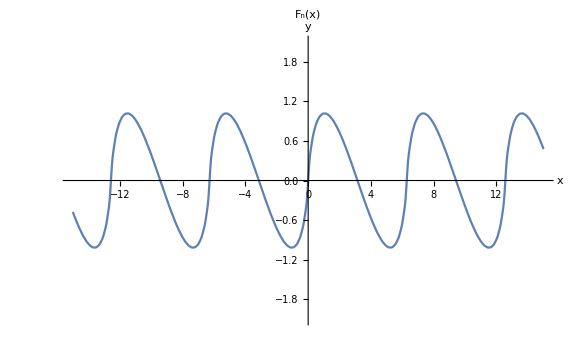

```mathematica
fn[x_,n_]:=∑_(k=1)^n Sin[k x]/k^2
plotFun[fn[x,30],{{-15,15},{-2.1,2.1}},{},"StyleBox[SubscriptBox[\"F\", \"n\"],FontSlant->\"Italic\"]StyleBox[\"(\",FontSlant->\"Italic\"]StyleBox[\"x\",FontSlant->\"Italic\"]StyleBox[\")\",FontSlant->\"Italic\"]"]
```

```mathematica
Manipulate[plotFun[fn[x,n],{{-15,15},{-2.1,2.1}},{},"F_n(x)"],{n,1,30,1,Appearance->"Open"},SaveDefinitions->True,Initialization:>{fn[x_,n_]:=∑_(k=1)^n Sin[k x]/k^2,plotFun[fun_,lims_,epilog_,label_,legs_:None]:=Framed@Plot[fun,{x,lims[[1,1]],lims[[1,2]]},PlotRange->{Full,{lims[[2,1]],lims[[2,2]]}},Epilog->epilog,PlotLegends->legs,PlotLabel->Style[label,Black,Bold,20],ImageSize->Large,AxesLabel->{"x","y"},BaseStyle->{FontSize->20}]}]
```

## e)

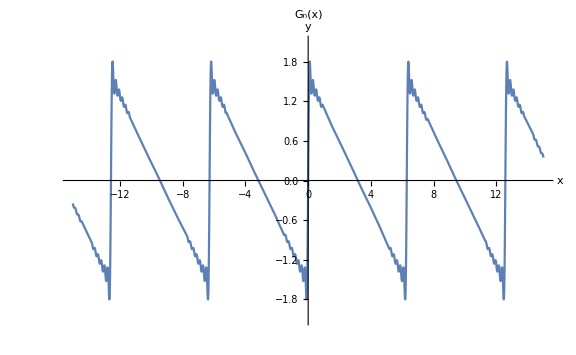

```mathematica
gn[x_,n_]:=∑_(k=1)^n Sin[k x]/k
plotFun[gn[x,30],{{-15,15},{-2.1,2.1}},{},"G_nStyleBox[\"(\",FontSlant->\"Italic\"]StyleBox[\"x\",FontSlant->\"Italic\"]StyleBox[\")\",FontSlant->\"Italic\"]"]
```

```mathematica
Manipulate[plotFun[gn[x,n],{{-15,15},{-2.1,2.1}},{},"G_n(x)"],{n,1,50,1,Appearance->"Open"},SaveDefinitions->True,Initialization:>{gn[x_,n_]:=∑_(k=1)^n Sin[k x]/k,plotFun[fun_,lims_,epilog_,label_,legs_:None]:=Framed@Plot[fun,{x,lims[[1,1]],lims[[1,2]]},PlotRange->{Full,{lims[[2,1]],lims[[2,2]]}},Epilog->epilog,PlotLegends->legs,PlotLabel->Style[label,Black,Bold,20],ImageSize->Large,AxesLabel->{"x","y"},BaseStyle->{FontSize->20}]}]
```

The Reihe seems to converge. What does the “Konvergenzkriterium von Weierstraß” say about it?

Let  g_k(x):=(sin(k x))/k with D = ℝ. For this we get:

sup_(x∈D) Abs[g_n(x)]=sup_(x∈D) Abs[(sin(k x))/k]

Function sin(k x) is stetig, therefore assumes its supremum, which is equal to 1. We can choose x=π/2 1/k, because then sin(k x)=sin(k π/2 1/k)=sin(π/2)=1. We have:

sup_(x∈D) Abs[(sin(k x))/k]=1/k

But Reihe ∑_(k=1)^∞ 1/k diverges, see the Skriptum. The “Konvergenzkriterium von Weierstraß” thus cannot be used to determine whether the Reihe of functions converges or not.

# 2) Ableitung

a) f(x)=(cos(x))^3

b) f(x)=(sin(1/x^2))^2

c) f(x)=(1+x)^2/(1-x)^3

f'(x)=?

#### Useful formulas

Ableitung of Sin and Cos

cos'(x)=-sin(x)
sin'(x)=cos(x)

Ableitung of a composite function (Satz 11.3)

(g ◦ f)'(x)=g'(f(x))·f'(x)

Ableitung of a product of functions

(f·g)'(x)=f'(x)·g(x)+f(x)·g'(x)

Ableitung of a “monomial function”

(α x^n)'=α n x^(n-1) , where α is a constant and n∈ℕ\{0}

Ableitung of a sum of two functions

(f+g)'(x)=f'(x)+g'(x)

## Solution

## a)

((cos(x))^3)'=3(cos(x))^2·(-sin(x))=-3 sin(x)·(cos(x))^2

## b)

((sin(1/x^2))^2)'=2sin(1/x^2)·cos(1/x^2)·(-2 1/x^3)=-4/x^3 sin(1/x^2)·cos(1/x^2)=-2/x^3sin(2/x^2)

## c)

((1+x)^2/(1-x)^3)'=((1+x)^2)' 1/(1-x)^3+(1+x)^2(1/(1-x)^3)'=2(1+x)1/(1-x)^3+(1+x)^2(3/(1-x)^4)=(2(1+x)(1-x)+3(1+x)^2)/(1-x)^4=(1+x)(2(1-x)+3(1+x))/(1-x)^4=((1+x)(5+x))/(1-x)^4

# 3) Ableitung von Sinh und Cosh

sinh'(x)=cosh(x) ?
cosh'(x)=sinh(x) ?

a) calculate using the definitions of sinh and cosh and Ableitung of the exponential function

b) calculate using the definition of an Ableitung

#### Useful formulas

Definitions of Sinh and Cosh

sinh(x)=(ⅇ^x-ⅇ^-x)/2
cosh(x)=(ⅇ^x+ⅇ^-x)/2

Ableitung of the exponential function

(ⅇ^x)'=ⅇ^x

Ableitung of a sum of two functions

(f+g)'(x)=f'(x)+g'(x)

Subtraction of sinh and cosh values

sinh(x)-sinh(y)=2 cosh((x+y)/2)sinh((x-y)/2)

cosh(x)-cosh(y)=2 sinh((x+y)/2)sinh((x-y)/2)

Ableitung of a function (Definition 11.1)

f'(x_0):=lim_(x→x_0) (f(x)-f(x_0))/(x-x_0)

Restgliedabschätzung für die komplexe Exponentialfunktion

exp(x)=∑_(n=0)^N x^n/(n!)+R_(N+1)(x),

Abs[R_(N+1)(x)]≤2 Abs[x]^(N+1)/((N+1)!),  Abs[x]≤N/2+1

## Solution

## a)

Using, among other things, the formula for Ableitung of a sum of functions and the definition of sinh we obtain:

sinh'(x)=((ⅇ^x-ⅇ^-x)/2)'=1/2((ⅇ^x)'-(ⅇ^-x)')=1/2(ⅇ^x-ⅇ^-x(-1))=1/2(ⅇ^x+ⅇ^-x)=cosh(x)

Analogously:

cosh'(x)=((ⅇ^x+ⅇ^-x)/2)'=1/2((ⅇ^x)'+(ⅇ^-x)')=1/2(ⅇ^x+ⅇ^-x(-1))=1/2(ⅇ^x-ⅇ^-x)=sinh(x)

## b)

By definition:

sinh'(x_0):=lim_(x→x_0) (sinh(x)-sinh(x_0))/(x-x_0)

We expand the Zähler using the “sinh(x)-sinh(y)” formula:

lim_(x→x_0) (sinh(x)-sinh(x_0))/(x-x_0)=lim_(x→x_0) (2 cosh((x+x_0)/2)sinh((x-x_0)/2))/(x-x_0)=lim_(x→x_0) (cosh((x+x_0)/2))·lim_(x→x_0) (sinh((x-x_0)/2))/((x-x_0)/2)

Cosh is a stetige function (it is a sum of two exponentials, which are themselves stetig) and so the limit for x→x_0 is equal to the function value at x_0. In other words:

lim_(x→x_0) (cosh((x+x_0)/2))=cosh((x_0+x_0)/2)=cosh(x_0)

Furthermore:

lim_(x→x_0) (sinh((x-x_0)/2))/((x-x_0)/2)=lim_(y→0) (sinh(y))/y for y=(x-x_0)/2

Limit lim_(y→0) (sinh(y))/y is actually an Ableitung of sinh at zero as lim_(y→0) (sinh(y))/y=lim_(y→0) (sinh(y)-sinh(0))/(y-0). To calculate that we have to resort either to the result of a) or to the “Restgliedabschätzung für die komplexe Exponentialfunktion”. We want to show that lim_(y→0) (sinh(y))/y=1. To that end let us consider the following expression:

|(sinh(y))/y-1|=|(ⅇ^y-ⅇ^-y)/(2y)-1|=1/(2|y|)|(1+y+R_2(y))-(1-y+R_2(-y))-2y|=1/(2|y|)|R_2(y)-R_2(-y)|

From the triangle inequality and Restgliedabschätzung property we get:

1/(2|y|)|R_2(y)-R_2(-y)|≤1/(2|y|)(|R_2(y)|+|R_2(-y)|)≤1/(2|y|)(2(|y|^2)/(2!)+2(|-y|^2)/(2!))=|y|

In total:

|(sinh(y))/y-1|≤|y|

When we apply the limit lim_(y→0)  to the right-hand side, it goes to zero. Therefore:

lim_(y→0) |(sinh(y))/y-1|=0

from where

lim_(y→0) (sinh(y))/y=1

as we wanted to prove. For cosh'(x_0) we would proceed analogously.

# 4) Gauß-sche Glockenfunktion

ψ(x)=ⅇ^(-x^2/(2 a^2))

a≠0 constant

ψ'(x)=?
ψ''(x)=?

#### Useful formulas

Ableitung of a composite function (Satz 11.3)

(g ◦ f)'(x)=g'(f(x))·f'(x)

Ableitung of the exponential function

(ⅇ^x)'=ⅇ^x

Ableitung of a “monomial function”

(α x^n)'=α n x^(n-1) , where α is a constant and n∈ℕ\{0}

Ableitung of a product of functions

(f·g)'(x)=f'(x)·g(x)+f(x)·g'(x)

## Plot

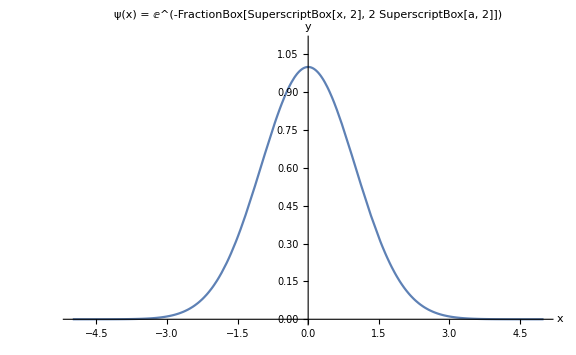

```mathematica
plotFun[ⅇ^(-x^2/(2 1.^2)),{{-5,5},{0,1.1}},{},"ψ(x) = ⅇ^(-FractionBox[SuperscriptBox[x, 2], 2 SuperscriptBox[a, 2]])"]
```

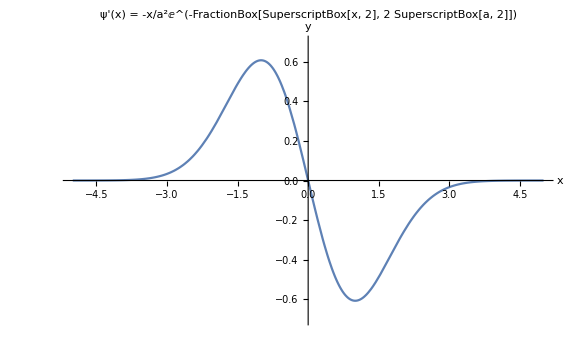

```mathematica
plotFun[With[{a=1.},-x/a^2 ⅇ^(-x^2/(2 a^2))],{{-5,5},{-0.7,0.7}},{},"ψ'(x) = -x/a^2ⅇ^(-FractionBox[SuperscriptBox[x, 2], 2 SuperscriptBox[a, 2]])"]
```

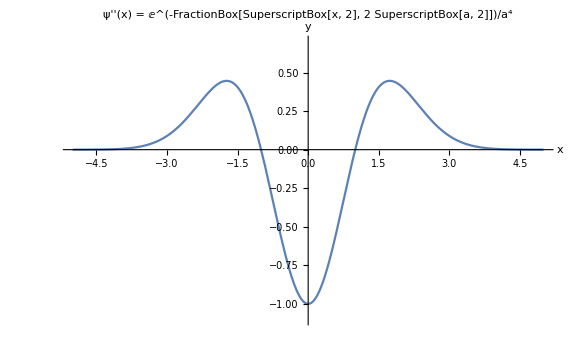

```mathematica
plotFun[With[{a=1.},(ⅇ^(-x^2/(2 a^2)) (x^2-a^2))/a^4],{{-5,5},{-1.1,0.7}},{},"ψ''(x) = ⅇ^(-FractionBox[SuperscriptBox[x, 2], 2 SuperscriptBox[a, 2]])/a^4"]
```

## Solution

We get:

ψ'(x)=(ⅇ^(-x^2/(2 a^2)))'=ⅇ^(-x^2/(2 a^2))·(-1/(2 a^2))2x=-x/a^2 ⅇ^(-x^2/(2 a^2))=-x/a^2ψ(x)

where we used the formula for Ableitung of composite functions and formulas for Ableitung of the exponential function and monomial functions. Similarly:

ψ''(x)=(-x/a^2ψ(x))'=(-1/a^2)ψ(x)+(-x/a^2)ψ'(x)=(-1/a^2)ψ(x)+(-x/a^2)(-x/a^2ψ(x))=(-1/a^2)ψ(x)(1-x^2/a^2)=((x^2-a^2)/a^4)ψ(x)=((x^2-a^2)/a^4)ⅇ^(-x^2/(2 a^2))

where the formula for Ableitung of a product of functions and the result for ψ'(x) were used.

# 5) Schrödinger-Gleichung

-ℏ^2/(2m)ψ''(x)+1/2 m ω^2 x^2 ψ(x)=E ψ(x)

## Solution

We substitute results of the previous exercise to the equation, specifically:

ψ(x)=ⅇ^(-x^2/(2 a^2))
ψ''(x)=-1/a^2(1-x^2/a^2)ⅇ^(-x^2/(2 a^2))=-1/a^2(1-x^2/a^2)ψ(x)

Then:

-ℏ^2/(2m)(-1/a^2(1-x^2/a^2)ψ(x))+1/2 m ω^2 x^2 ψ(x)=E ψ(x)

which can be simplified into:

ℏ^2/(2m a^2)(1-x^2/a^2)ψ(x)+1/2 m ω^2 x^2 ψ(x)=E ψ(x)

We can divide both sides by ψ(x) and simplify further to get:

(ℏ^2/(2m a^2)-E)+x^2(1/2 m ω^2-ℏ^2/(2m a^4))=0

This equation has to be satisfied for all x and so the two coefficients have to be zero:

ℏ^2/(2m a^2)-E=0  ∧  1/2 m ω^2-ℏ^2/(2m a^4)=0

After slight simplification:

E=ℏ^2/(2m a^2)  ∧  m^2 ω^2=ℏ^2/a^4

from where we get:

a=√(ℏ/(m ω)) and E=1/2 ℏ ω